## Distortion Operator Calculation Benchmark

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/mkononen/git/quantum-utils-mathematica/test/benchmarks/GRAPE

```mathematica
Needs["QuantumUtils`"]
Needs["StripLineResonator`"]
```

```mathematica
LaunchKernels[]
```

LaunchKernels::nodef: Some subkernels are already running. Not launching default kernels again.

$Failed

### Parameters

```mathematica
maxVoltage=1(*V*);
γe=2.8*10^6*2*π;

SelectMode[$onePort];

Parameters[$onePort,"linear"]={
	l->168.9pH,                 
	r->0.01Ω,
	c->1.47856 pF,
	cm->0.021256 pF,
	rs->50Ω,
	scale->19*0.838 10^11 MHz/Wb (* Calibrated to give 360 rotation in 100 ns (10 MHz Rabi) at full Pulse Amplitude*)
};

Parameters[$onePort,"nonlinear"]={
	l->168.9pH * (1+αL*Abs[il]^2),
	r->0.01Ω,
	c->1.47856 pF,
	cm->0.021256 pF,
	rs->50Ω,
	scale->1.9*0.838 10^12 MHz/Wb (* Calibrated to give 360 rotation in 100 ns (10 MHz Rabi) at full Pulse Amplitude*) (*NOTE: I've changed from 0.838 10^11 to ^13*)
}/.{
	αL->(0.01/amp^2)
};
```

```mathematica
ω1= 10γe;
ωc = 3500γe;
ω0 = 3200γe;
dt = 5.0ns;
```

### Create initial pulse

#### Parameters

```mathematica
controlRange = 1.{{ ω0+50*2.8 *10^6*2*π,ωc+25*2.8 *10^6*2*π}}; 
ta = 750*10^-9;Nta = IntegerPart[ta/dt ];
tp=300*10^-9; Ntp = IntegerPart[tp/dt];
dtran = 0.01;Ntr = 100;
```

#### Pulse for ω_0

```mathematica
auxRange = 1.{{ 0,30*2.8 *10^6*2*π}}; 
auxiliarPulse = RandomSmoothPulse[dt,Nta+1,auxRange];
auxiliarPulse[[All,2]]=MapThread[Times,{GaussianTailsPulse[dt,ta,ta/4,Max->1][[All,2]],auxiliarPulse[[All,2]]}] +ωc-30*2.8 *10^6*2*π;
```

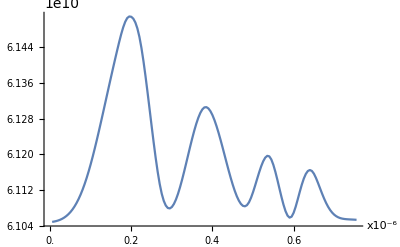

```mathematica
ListLinePlot[auxiliarPulse[[All,2]],Ticks->{Transpose[{Range[0,Length[auxiliarPulse],20],N[dt*10^6*Range[0,Length[auxiliarPulse],20]]}],Automatic},AxesLabel->{"x10^-6",None}]
```

```mathematica
(*Create gaussian tails*)
GaussianEnvelope = GaussianTailsPulse[dt,tp,tp/7,Max->ωc-30*2.8 *10^6*2*π-ω0]+ω0;
```

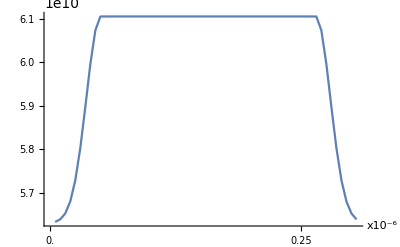

```mathematica
ListLinePlot[GaussianEnvelope[[All,2]],Ticks->{Transpose[{Range[0,Length[GaussianEnvelope],50],N[dt*10^6*Range[0,Length[GaussianEnvelope],50]]}],Automatic},AxesLabel->{"x10^-6",None}]
```

```mathematica
(*Merge the two pulses to create the initial guess*)
Pulseω0 = RandomSmoothPulse[dt,Ntp+1,auxRange]; Pulseω0[[All,2]]=GaussianEnvelope[[All,2]];
Pulseω0[[75;;375,2]]=auxiliarPulse[[All,2]];
```

Set::take: Cannot take positions 75 through 375 in {{5.×10^-9,5.63281×10^10},{5.×10^-9,5.63852×10^10},{5.×10^-9,5.65194×10^10},{5.×10^-9,5.67941×10^10},{5.×10^-9,5.72803×10^10},{5.×10^-9,5.80182×10^10},«40»,{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},«11»}.

```mathematica
ListLinePlot[Pulseω0[[All,2]],Ticks->{Transpose[{Range[0,Length[Pulseω0],50],N[dt*10^6*Range[0,Length[Pulseω0],50]]}],Automatic},AxesLabel->{"x10^-6",None}]
```

-Graphics-

```mathematica
tab = { {TextCell[""],TextCell["gate Pulse"],TextCell["gate Pulse (gate)"],TextCell["What we want (total)"],TextCell["What we want (gate)"]},
	 {TextCell["Max val"],Max[Pulseω0[[All,2]]],Max[Pulseω0[[50;;150,2]]],ωc+30*2.8 *10^6*2*π,ωc+30*2.8 *10^6*2*π},
	   {TextCell["Min val"],Min[Pulseω0[[All,2]]],Min[Pulseω0[[50;;150,2]]],ω0,ωc-30*2.8 *10^6*2*π}};
Grid[tab,Frame->All]
(*Add constant ω0 term to the ω0 Pulse*)
Pulseω0=Join[Table[{1/(2*10^8),Pulseω0[[1,2]]},{x,1,Ntr+0.2*Ntr,1}],Pulseω0];
Pulseω0=Join[Pulseω0,Table[{1/(2*10^8),Pulseω0[[1,2]]},{x,1,Ntr-0.2*Ntr,1}]];
```

Part::take: Cannot take positions 50 through 150 in {{5.×10^-9,5.63281×10^10},{5.×10^-9,5.63852×10^10},{5.×10^-9,5.65194×10^10},{5.×10^-9,5.67941×10^10},{5.×10^-9,5.72803×10^10},{5.×10^-9,5.80182×10^10},«40»,{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},«11»}.

| gate Pulse | gate Pulse (gate) | What we want (total) | What we want (gate)
Max val | 6.10474×10^10 | {{5.×10^-9,5.63281×10^10},{5.×10^-9,5.63852×10^10},{5.×10^-9,5.65194×10^10},{5.×10^-9,5.67941×10^10},{5.×10^-9,5.72803×10^10},{5.×10^-9,5.80182×10^10},{5.×10^-9,5.89627×10^10},{5.×10^-9,5.99496×10^10},{5.×10^-9,6.07249×10^10},{5.×10^-9,6.10459×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10459×10^10},{5.×10^-9,6.07249×10^10},{5.×10^-9,5.99496×10^10},{5.×10^-9,5.89627×10^10},{5.×10^-9,5.80182×10^10},{5.×10^-9,5.72803×10^10},{5.×10^-9,5.67941×10^10},{5.×10^-9,5.65194×10^10},{5.×10^-9,5.63852×10^10}}⟦50;;150,2⟧ | 6.2103×10^10 | 6.2103×10^10
Min val | 5.63281×10^10 | {{5.×10^-9,5.63281×10^10},{5.×10^-9,5.63852×10^10},{5.×10^-9,5.65194×10^10},{5.×10^-9,5.67941×10^10},{5.×10^-9,5.72803×10^10},{5.×10^-9,5.80182×10^10},{5.×10^-9,5.89627×10^10},{5.×10^-9,5.99496×10^10},{5.×10^-9,6.07249×10^10},{5.×10^-9,6.10459×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10459×10^10},{5.×10^-9,6.07249×10^10},{5.×10^-9,5.99496×10^10},{5.×10^-9,5.89627×10^10},{5.×10^-9,5.80182×10^10},{5.×10^-9,5.72803×10^10},{5.×10^-9,5.67941×10^10},{5.×10^-9,5.65194×10^10},{5.×10^-9,5.63852×10^10}}⟦50;;150,2⟧ | 5.62973×10^10 | 6.10474×10^10

```mathematica
Length[auxiliarPulse]
Length[GaussianEnvelope]
```

151

61

#### Parameters

```mathematica
controlRange = 1.{{ ω0+50*2.8 *10^6*2*π,ωc+25*2.8 *10^6*2*π}}; 
ta = 750*10^-9;Nta = IntegerPart[ta/dt ];
tp=300*10^-9; Ntp = IntegerPart[tp/dt];
dtran = 0.01;Ntr = 100;
```

#### Pulse for ω_1 (x-direction)

```mathematica
f[x_] =Piecewise[{{0,x<100},{1,700>x>100}}];
g[x_] = PiecewiseExpand[Piecewise[{{f[x],x<700},{0,x>700}}]];
```

```mathematica
Plot[g[x],{x,0,800}]
```

#### Initial Guess

```mathematica
initialGuess=Table[{5ns,g[i],0.,Pulseω0[[i,2]]},{i,1,Ntp+2*Ntr+1}];
Ntotal=Length[initialGuess]
```

261

```mathematica
{First@@PulsePlot[ToPulse[initialGuess],PlotRange-> {All,{0,1}},AspectRatio-> 1/3],Last@@PulsePlot[ToPulse[initialGuess],PlotRange-> {All,{ω0-10*2.8*π*10^6,ωc+30*2.8*π*10^6}},AspectRatio-> 1/3]}
```

### Distortion operators

```mathematica
samplingRate=2.5ns;
ringdownTime=100ns;
controlRange = maxVoltage*{{-1,1},{-1,1}};  
τc=10^-8;
```

```mathematica
ClearAll@ringDownDistortion;
ringDownDistortion=
ResonatorRingdownDistortion[
1, (* I believe this is the number of compensation steps? *)
Parameters["nonlinear"],
CompensationTimeSteps->{ringdownTime}, (* this is equivalent to ringdownTime in linear example when DecayRatio is set to 0 *) 
DecayRatio->0, (* Setting this to zero eliminates ringdown compensation *)
RiseTime->0.2ns,
SamplingInterval->samplingRate,
MaxSteps->10^6,
AmplitudeRange->controlRange
];
```

```mathematica
Clear[distortion]
distortion=DistortionOperator[
Function[{pulse,computeJac},
Module[{zpulse,xypulse,M,L,N,K,f,AUX,x,zdistortion},
xypulse=ringDownDistortion[pulse⟦All,1;;3⟧,computeJac];
If[computeJac,
{
{M,L,N,K}=Dimensions[xypulse⟦2⟧];

zdistortion=ExponentialDistortion[τc,Length[pulse],M,pulse⟦1,1⟧,samplingRate];
zpulse=zdistortion[pulse⟦All,{1,4}⟧,computeJac];

Append[xypulse⟦1⟧ᵀ,zpulse⟦1,All,2⟧]ᵀ,

f=Function[x,Transpose[Append[Transpose[ArrayReshape[x,{L+1,K}]],{0.,0.,0.}]]];
AUX=Transpose[xypulse⟦2⟧,{1,3,2,4}];
Table[AUX⟦i,j⟧={AUX⟦i,j⟧},{i,1,M},{j,1,N}];
AUX=Apply[f,AUX,{2}];
Table[AUX⟦i,j⟧⟦L+1,K+1⟧=ArrayReshape[ArrayReshape[zpulse⟦2⟧,{1,N*M}]⟦1⟧,{M,N}]⟦i,j⟧,{i,1,M},{j,1,N}];
Transpose[AUX,{1,3,2,4}] 
},
 M=Length[xypulse];

zdistortion=ExponentialDistortion[τc,Length[pulse],M,pulse⟦1,1⟧,samplingRate];
zpulse=zdistortion[pulse⟦All,{1,4}⟧,computeJac];

Append[xypulseᵀ,zpulse⟦All,2⟧]ᵀ
]
]
],
"JointDistortion"
]
```

JointDistortion

```mathematica
distortedPulse=distortion[initialGuess,False]; //AbsoluteTiming
Dimensions[Last@distortedPulse]
```

{32.6426,Null}

{4}

```mathematica
Profile[distortion[initialGuess, False]]
```

StringForm::string: String expected at position 1 in StringForm[«3»].

StringForm::string: String expected at position 1 in StringForm[tr[«1»],«2»,«2»].

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

{{2.5×10^-9,0.,0.,6.61872×10^9},561,{2.5×10^-9,-360972.,-104066.,8.48548×10^-38+199+0.0000157645 {{5.×10^-9,5.63281×10^10},{5.×10^-9,5.63852×10^10},{5.×10^-9,5.65194×10^10},56,{5.×10^-9,5.65194×10^10},{5.×10^-9,5.63852×10^10}}⟦261,2⟧}}
 |  |  |  |

```mathematica
plt1=First@@PulsePlot[ToPulse[distortedPulse],PlotRange-> {All,{-1,1.2*10^8}},AspectRatio-> 1/3,PlotLabel-> "Distorted Initial Control X"];
plt2=Last@Take[First@PulsePlot[ToPulse[distortedPulse],PlotRange-> {All,{1,-1.2*10^8}},AspectRatio-> 1/3,PlotLabel-> "Distorted Initial Control Y"],2];
plt3=Last@@PulsePlot[ToPulse[distortedPulse],PlotRange-> {All,{ω0-10*2.8*π*10^6,ωc+30*2.8*π*10^6}},AspectRatio-> 1/3,PlotLabel-> "Distorted Initial Control Z"];
```

```mathematica
GraphicsGrid[{{plt1},{plt2},{plt3}}]
```